Sebastian Murk (sebastian.murk@oist.jp) [ORCID ID: 0000-0001-7296-0420]

Quantum Gravity Unit, Okinawa Institute of Science and Technology, 1919-1 Tancha, Onna-son, Okinawa 904-0495, Japan

Daniel R. Terno (daniel.terno@mq.edu.au) [ORCID ID: 0000-0002-0779-0100]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

Rama Vadapalli (venkataramaraju.vadapalli@students.mq.edu.au) [ORCID ID: 0000-0001-7470-1342]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

```mathematica
ClearAll["`*"]; 
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
Solve[1/(1/P[z]-(Q[z]-P[z]+3rg)/(4rg P[z])(1+Cos[A]))==100z/.{z->50,rg->1},A]
```

{{A→ConditionalExpression[-ArcCos[(7 (182-25 √53))/(25 (-47+7 √53))]+2 π C[1], C[1]∈ℤ]},{A→ConditionalExpression[ArcCos[(7 (182-25 √53))/(25 (-47+7 √53))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
N[-ArcCos[(7 (182-25 √53))/(25 (-47+7 √53))]+2 π ]
```

4.71219

## Setup

```mathematica
ClearAll["`*"];
```

```mathematica
f[r_]:=1-rg/r
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
k[z_]:=√((Q[z]-P[z]+3rg)/(2Q[z]));
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
L[z_]:=𝒟[z];
B3[z_]:=(2 rg P[z])/(P[z]-rg+Q[z]);
Subscript[ϕ, 0][z_,χ_]:=2 √(P[z]/Q[z])(EllipticK[k[z]]-EllipticF[χ/2,k[z]]);
Subscript[r, 0][z_,χ_]:=1/(1/P[z]-(Q[z]-P[z]+3rg)/(4rg P[z])(1+Cos[χ]));
Subscript[x, 0][z_,χ_]:=Subscript[r, 0][z,χ]Cos[Subscript[ϕ, 0][z,χ]];
Subscript[y, 0][z_,χ_]:=Subscript[r, 0][z,χ]Sin[Subscript[ϕ, 0][z,χ]];
Subscript[χ, ∞][z_]:=2ArcSin[√((Q[z]-P[z]+rg)/(Q[z]-P[z]+3rg))];
χ[z_]:=ϵ Subscript[χ, ∞][z];
Subscript[r, in][z_]:=Subscript[r, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[ϕ, in][z_]:=Subscript[ϕ, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
Subscript[ϕd, in][z_]:=L[z]/(Subscript[r, in][z])^2;
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
```

```mathematica
dchdph[z_,chi_]:=-(Sqrt[Q[z]/P[z](1-k[z]^2 Sin[chi/2]^2)])
dchds[z_,chi_]:=-L[z]/Subscript[r, 0][z,chi]^2 dchdph[z,chi]
ϕot[z_]:=Subscript[ϕ, 0][z,Subscript[χ, ∞][z]];
dchds2d[z_,chi_]:=-1/(1024 rg^2 (-1+z) z^2)(3-z+√((-1+z) (3+z))) (-1-z+√((-1+z) (3+z))+(3-z+√((-1+z) (3+z))) Cos[chi])^3 (3 z+13 (-1+√((-1+z) (3+z)))+5 (3-z+√((-1+z) (3+z))) Cos[chi]) Sin[chi]
apf[z_,chi_]:=Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]
pf[z_,chi_]:=If[chi<Pi, -Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2],Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]]
```

```mathematica
lhs2chi=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var[chi];
rf2chi[z_,chi_]:=1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 (1/rg^2 12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]+1/(rg (-1+z))(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])-(32 (-1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]) (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])))
rf2chiR[z_,chi_]:=1/(2048 rg^4 z^(7/2))3 √(1/(-1+z)) (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^5 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]
```

```mathematica
ϵ=1.0001;
epout=1.;
chimax=4.71219476938052;
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;
s=1;
om=1; 
z=10.;
```

```mathematica
sol2dchi=NDSolve[{lhs2chi==rf2chi[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->12,WorkingPrecision->40]
var2c[chi_]:=var[chi]/.sol2dchi[[1]]
var2cd[chi_]:=var'[chi]/.sol2dchi[[1]]
var2cdd[chi_]:=var''[chi]/.sol2dchi[[1]]
```

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (40.).

{{var→InterpolatingFunction[…]}}

```mathematica
N[var2c[chimax]]
```

0.00163223-4.3282×10^-14 ⅈ

```mathematica
lhs2chi0=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2);
rf2chi[z_,chi_]:=1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 (1/rg^2 12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]+1/(rg (-1+z))(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])-(32 (-1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]) (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])))
```

```mathematica
stu0c=NDSolve[{lhs2chi0==rf2chi[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var0[t_]:=var[t]/.stu0c[[1]]
vard0[t_]:=var'[t]/.stu0c[[1]]
vardd0[t_]:=var''[t]/.stu0c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
stu1c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var0[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var1[t_]:=var[t]/.stu1c[[1]]
vard1[t_]:=var'[t]/.stu1c[[1]]
vardd1[t_]:=var''[t]/.stu1c[[1]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
stu2c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var1[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var2[t_]:=var[t]/.stu2c[[1]]
var2d[t_]:=var'[t]/.stu2c[[1]]
var2dd[t_]:=var''[t]/.stu2c[[1]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
stu3c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var2[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var3[t_]:=var[t]/.stu3c[[1]]
var3d[t_]:=var'[t]/.stu3c[[1]]
var3dd[t_]:=var''[t]/.stu3c[[1]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
stu4c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var3[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var4[t_]:=var[t]/.stu4c[[1]]
var4d[t_]:=var'[t]/.stu4c[[1]]
var4dd[t_]:=var''[t]/.stu4c[[1]]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
stu5c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var4[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var5[t_]:=var[t]/.stu5c[[1]]
var5d[t_]:=var'[t]/.stu5c[[1]]
var5dd[t_]:=var''[t]/.stu5c[[1]]
vartheta[t_]:=var0[t]+var1[t]+var2[t]+var3[t]+var4[t]+var5[t]
```

NDSolve::precw: The precision of the differential equation ({«1»,{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

## Figures 1(a) and 3(a)

At  b1,
χ  = π

At ∞_(out),
χ = 2π-epout χ_∞[z]
 = 4.76045

```mathematica
(χ[z]+chimax)/2
2π-epout Subscript[χ, ∞][z]
```

3.11754

4.76045

### Figure 1(a): Plot of ω^θ

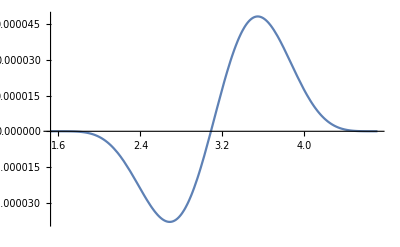

```mathematica
Plot[{rf2chi[z,chi]},{chi,χ[z],chimax},PlotRange->All]
```

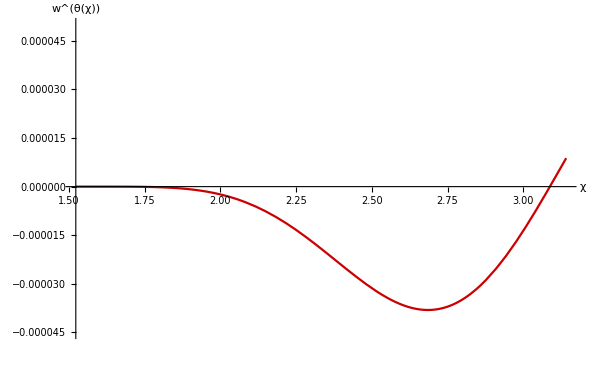

```mathematica
PlotIn=Plot[{rf2chi[z,chi]},{chi,χ[z],π},PlotRange->{Automatic,{-0.000045,0.00005}},PlotStyle->Darker[Red,0.2],AxesLabel->{"χ","w^(<θ(χ)>)"},TicksStyle->Directive[FontSize->12],ImageSize->600]
```

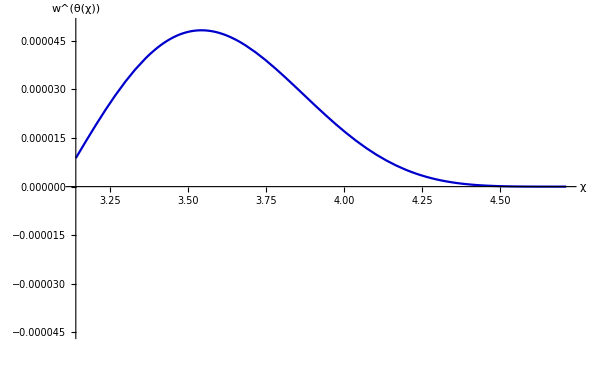

```mathematica
PlotOut=Plot[{rf2chi[z,chi]},{chi,π,chimax},PlotRange->{Automatic,{-0.000045,0.00005}},PlotStyle->Darker[Blue,0.2],AxesLabel->{"χ","w^(<θ(χ)>)"},TicksStyle->Directive[FontSize->12],ImageSize->600]
```

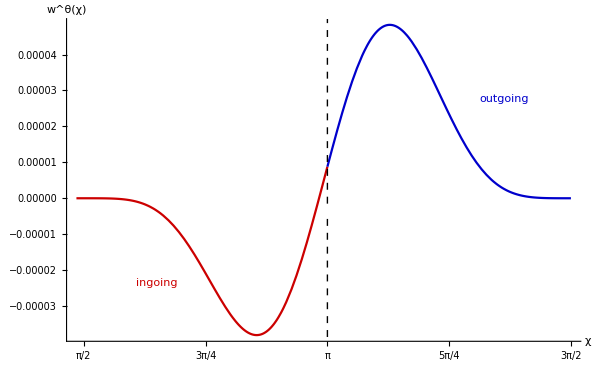

```mathematica
Show[PlotIn,PlotOut,PlotRange->{{1.5,4.8},{-0.0000435,Automatic}},AxesOrigin->{1.45,0},AxesLabel->{"χ","w^θ(χ)"},LabelStyle->Directive[Black],Ticks->{{{π/2,"π/2"},{3π/4,"3π/4"},{π,"π"},{5π/4,"5π/4"},{3π/2,"3π/2"}},Automatic},TicksStyle->Directive[FontSize->15],ImageSize->605,Epilog->{Inset[Style["ingoing",Darker[Red,0.2]],Scaled[{0.175,0.18}]],Inset[Style["outgoing",Darker[Blue,0.2]],Scaled[{0.85,0.75}]],Directive[Thickness->0.002,Black,Dashed],Line[{{π,-0.0000015},{π,0.00045}}],Directive[Thickness->0.002,Black,Dashed],Line[{{π,-0.00000575},{π,-0.00045}}]}]
```

### Figure 3(a): Plot comparing ϑ, ϑ_0, ϑ_0+ϑ_1, ϑ_0+ϑ_1+ϑ_2, ϑ_0+ϑ_1+ϑ_2+ϑ_3

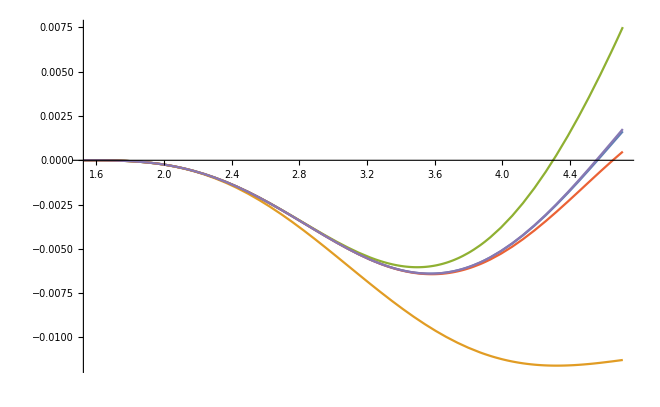

```mathematica
Plot[{vartheta[chi],var0[chi],var0[chi]+var1[chi],var0[chi]+var1[chi]+var2[chi],var0[chi]+var1[chi]+var2[chi]+var3[chi]},{chi,χ[z],chimax},PlotRange->All]
```

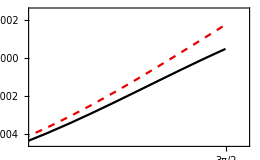

```mathematica
ϑ2ϑ3inset=Plot[{var0[chi]+var1[chi]+var2[chi],var0[chi]+var1[chi]+var2[chi]+var3[chi]},{chi,χ[z],chimax},PlotRange->{{4.15,4.77},{-0.0045,0.0025}},FrameTicks->{{{-0.004,-0.002,{0.000,"0.000"},0.002},None},{{{3π/2,"3π/2"}},None}},FrameTicksStyle->Directive[FontSize->14],PlotStyle->{Black,{Darker[Red,0.1],Dashed}},Frame->True,ImageSize->260]
```

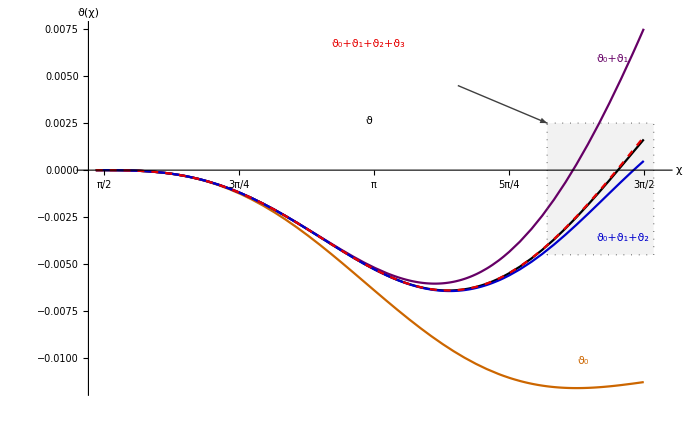

```mathematica
Plot[{vartheta[chi],var0[chi],var0[chi]+var1[chi],var0[chi]+var1[chi]+var2[chi],var0[chi]+var1[chi]+var2[chi]+var3[chi]},{chi,χ[z],chimax},AxesLabel->{"χ","ϑ(χ)"},LabelStyle->Directive[Black],PlotRange->{{1.48,4.81},All},PlotStyle->{Black,Darker[Orange,0.2],Darker[Purple,0.2],Darker[Blue,0.2],{Darker[Red,0.1],Dashed}},TicksStyle->Directive[FontSize->15],Ticks->{{{π/2,"π/2"},{3π/4,"3π/4"},{π,"π"},{5π/4,"5π/4"},{3π/2,"3π/2"}},Automatic},ImageSize->700,Prolog->{Opacity[0.10,Gray],Rectangle[{4.15,-0.0045},{4.77,0.0025}]},Epilog->{Inset[ϑ2ϑ3inset,Scaled[{0.47,0.805}]],Inset[Style["ϑ",Black],Scaled[{0.49,0.735}]],Inset[Style["ϑ_0",Darker[Orange,0.2]],Scaled[{0.85,0.0925}]],Inset[Style["ϑ_0+ϑ_1",Darker[Purple,0.2]],Scaled[{0.9,0.90}]],Inset[Style["ϑ_0+ϑ_1+ϑ_2",Darker[Blue,0.2]],Scaled[{0.9175,0.42}]],Inset[Style["ϑ_0+ϑ_1+ϑ_2+ϑ_3",{Darker[Red,0.1],Dashed}],Scaled[{0.49,0.94}]],Directive[Thickness->0.0013,Darker[Gray,0.5]],Arrowheads[0.025],Arrow[{{3.63,0.0045},{4.15,0.0025}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.15,-0.0045},{4.15,0.0025}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.77,-0.0045},{4.77,0.0025}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.15,-0.0045},{4.77,-0.0045}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.15,0.0025},{4.77,0.0025}}]}]
```

## Setup

```mathematica
ClearAll["`*"];
```

```mathematica
f[r_]:=1-rg/r
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
k[z_]:=√((Q[z]-P[z]+3rg)/(2Q[z]));
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
L[z_]:=𝒟[z];
B3[z_]:=(2 rg P[z])/(P[z]-rg+Q[z]);
Subscript[ϕ, 0][z_,χ_]:=2 √(P[z]/Q[z])(EllipticK[k[z]]-EllipticF[χ/2,k[z]]);
Subscript[r, 0][z_,χ_]:=1/(1/P[z]-(Q[z]-P[z]+3rg)/(4rg P[z])(1+Cos[χ]));
Subscript[x, 0][z_,χ_]:=Subscript[r, 0][z,χ]Cos[Subscript[ϕ, 0][z,χ]];
Subscript[y, 0][z_,χ_]:=Subscript[r, 0][z,χ]Sin[Subscript[ϕ, 0][z,χ]];
Subscript[χ, b1][z_]:=π;
χ[z_]:=ϵ Subscript[χ, b1][z];
Subscript[r, in][z_]:=Subscript[r, 0][z,ϵ Subscript[χ, b1][z]];
Subscript[ϕ, in][z_]:=Subscript[ϕ, 0][z,ϵ Subscript[χ, b1][z]];
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
Subscript[ϕd, in][z_]:=L[z]/(Subscript[r, in][z])^2;
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
```

```mathematica
dchdph[z_,chi_]:=-(Sqrt[Q[z]/P[z](1-k[z]^2 Sin[chi/2]^2)])
dchds[z_,chi_]:=-L[z]/Subscript[r, 0][z,chi]^2 dchdph[z,chi]
ϕot[z_]:=Subscript[ϕ, 0][z,Subscript[χ, b1][z]];
dchds2d[z_,chi_]:=-1/(1024 rg^2 (-1+z) z^2)(3-z+√((-1+z) (3+z))) (-1-z+√((-1+z) (3+z))+(3-z+√((-1+z) (3+z))) Cos[chi])^3 (3 z+13 (-1+√((-1+z) (3+z)))+5 (3-z+√((-1+z) (3+z))) Cos[chi]) Sin[chi]
apf[z_,chi_]:=Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]
pf[z_,chi_]:=If[chi<Pi, -Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2],Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]]
```

```mathematica
lhs2chi=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var[chi];
rf2chiR[z_,chi_]:=1/(2048 rg^4 z^(7/2))3 √(1/(-1+z)) (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^5 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]
```

```mathematica
ϵ=1.0001;
epout=1.;
chimax=2Pi-epout Subscript[χ, ∞][z];
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;
s=1;
om=1; 
z=10.;
```

```mathematica
sol2dchi=NDSolve[{lhs2chi==rf2chiR[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->12,WorkingPrecision->40]
var2c[chi_]:=var[chi]/.sol2dchi[[1]]
var2cd[chi_]:=var'[chi]/.sol2dchi[[1]]
var2cdd[chi_]:=var''[chi]/.sol2dchi[[1]]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 var[chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-2.07067×10^-6 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==1.54408×10^-7 (0.183346-«19» «1»)^5 If[chi<π,-√Plus[«2»],√(1+Times[«2»])],var[«18»]==0,var'[3.14191]==0},«3»,{}}) is less than WorkingPrecision (40.).

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.760445936315930103839497864125291157371.

{{var→InterpolatingFunction[{{3.141906812855152164587480001500807702541, 4.760445936315930103839497864125291157371}}, <>]}}

```mathematica
lhs2chi0=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2);
rf2chiR[z_,chi_]:=1/(2048 rg^4 z^(7/2))3 √(1/(-1+z)) (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^5 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]
```

```mathematica
stu0c=NDSolve[{lhs2chi0==rf2chiR[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var0[t_]:=var[t]/.stu0c[[1]]
vard0[t_]:=var'[t]/.stu0c[[1]]
vardd0[t_]:=var''[t]/.stu0c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{(21.9258 Power[«2»] If[«3»] Power[«2»]-2.07067×10^-6 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==1.54408×10^-7 (0.183346-3.81665 Cos[«1»])^5 If[chi<π,-√Plus[«2»],√(1+Times[«2»])],var[3.14191]==0,var'[3.14191]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010303686775599.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010303686775599}}, <>]}}

```mathematica
stu1c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var0[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var1[t_]:=var[t]/.stu1c[[1]]
vard1[t_]:=var'[t]/.stu1c[[1]]
vardd1[t_]:=var''[t]/.stu1c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«10002»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«9992»},{Automatic}][chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-«1») var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==0,«1»==0,var'[«18»]==0},«3»,{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76044593631593038196569978027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010294007948777.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010294007948777}}, <>]}}

```mathematica
stu2c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var1[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var2[t_]:=var[t]/.stu2c[[1]]
var2d[t_]:=var'[t]/.stu2c[[1]]
var2dd[t_]:=var''[t]/.stu2c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«10002»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«9992»},{Automatic}][chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-«1») var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==0,«1»==0,var'[«18»]==0},«3»,{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76044593631593038196569978027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010300773752055.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010300773752055}}, <>]}}

```mathematica
stu3c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var2[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var3[t_]:=var[t]/.stu3c[[1]]
var3d[t_]:=var'[t]/.stu3c[[1]]
var3dd[t_]:=var''[t]/.stu3c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«10002»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«9992»},{Automatic}][chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-«1») var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==0,«1»==0,var'[«18»]==0},«3»,{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76044593631593038196569978027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010300088238987.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010300088238987}}, <>]}}

```mathematica
stu4c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var3[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var4[t_]:=var[t]/.stu4c[[1]]
var4d[t_]:=var'[t]/.stu4c[[1]]
var4dd[t_]:=var''[t]/.stu4c[[1]]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«10002»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«9992»},{Automatic}][chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-«1») var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==0,«1»==0,var'[«18»]==0},«3»,{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76044593631593038196569978027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010308803025689.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010308803025689}}, <>]}}

```mathematica
stu5c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var4[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
var5[t_]:=var[t]/.stu5c[[1]]
var5d[t_]:=var'[t]/.stu5c[[1]]
var5dd[t_]:=var''[t]/.stu5c[[1]]
vartheta[t_]:=var0[t]+var1[t]+var2[t]+var3[t]+var4[t]+var5[t]
```

NDSolve::precw: The precision of the differential equation ({{111.111 (0.1+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«10002»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«9992»},{Automatic}][chi]+(21.9258 Power[«2»] If[«3»] Power[«2»]-«1») var'[chi]+120.185 (0.1+Times[«2»])^4 (1-0.176425 Power[«2»]) var''[chi]==0,«1»==0,var'[«18»]==0},«3»,{}}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76044593631593038196569978027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point chi == 4.76044593631593010317736304857.

{{var→InterpolatingFunction[{{3.14190681285515216458748000150, 4.76044593631593010317736304857}}, <>]}}

## Figures 1(b) and 3(b)

At  b1,
χ  = π

At ∞_(out),
χ = 2π-epout χ_∞[z]
 = 4.76045

### Figure 1(a): Plot of ω^θ

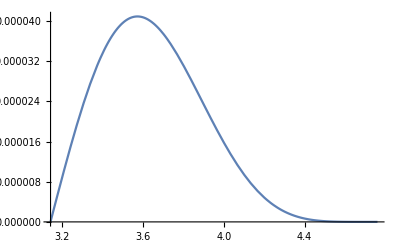

```mathematica
Plot[{rf2chiR[z,chi]},{chi,χ[z],chimax},PlotRange->All]
```

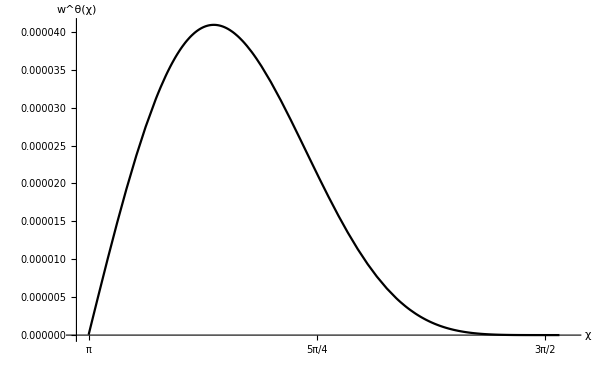

```mathematica
Plot[{rf2chiR[z,chi]},{chi,χ[z],chimax},PlotRange->{{3.1,4.8},Automatic},AxesLabel->{"χ","w^θ(χ)"},LabelStyle->Directive[Black],Ticks->{{{π,"π"},{5π/4,"5π/4"},{3π/2,"3π/2"}},Automatic},TicksStyle->Directive[FontSize->15],PlotStyle->Black,ImageSize->605]
```

### Figure 3(b): Plot comparing ϑ, ϑ_0, ϑ_0+ϑ_1, ϑ_0+ϑ_1+ϑ_2, ϑ_0+ϑ_1+ϑ_2+ϑ_3

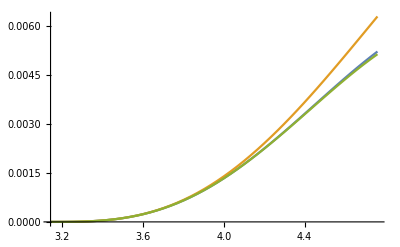

```mathematica
Plot[{var2c[chi],var0[chi],var0[chi]+var1[chi]},{chi,χ[z],chimax},PlotRange->All]
```

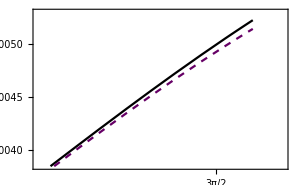

```mathematica
ϑ0ϑ1inset=Plot[{var2c[chi],var0[chi]+var1[chi]},{chi,χ[z],chimax},PlotRange->{{4.48,4.8},{0.00385,0.0053}},FrameTicks->{{{{0.004,"0.0040"},0.0045,{0.005,"0.0050"}},None},{{{3π/2,"3π/2"}},None}},FrameTicksStyle->Directive[FontSize->14],PlotStyle->{Black,{Darker[Purple,0.2],Dashed}},Frame->True,ImageSize->300]
```

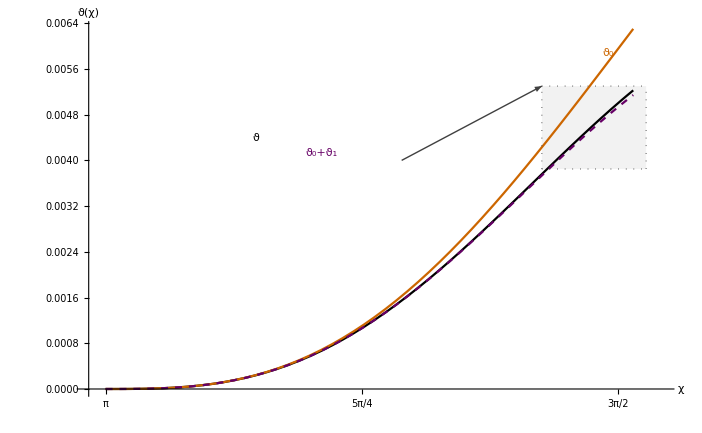

```mathematica
Plot[{var2c[chi],var0[chi],var0[chi]+var1[chi]},{chi,χ[z],chimax},AxesLabel->{"χ","ϑ(χ)"},LabelStyle->Directive[Black],PlotRange->{{3.09,4.85},Automatic},PlotStyle->{Black,Darker[Orange,0.2],{Darker[Purple,0.2],Dashed},Darker[Blue,0.2]},TicksStyle->Directive[FontSize->15],Ticks->{{{π,"π"},{5π/4,"5π/4"},{3π/2,"3π/2"}},Automatic},ImageSize->702,Prolog->{Opacity[0.10,Gray],Rectangle[{4.48,0.00385},{4.8,0.0053}]},Epilog->{Inset[ϑ0ϑ1inset,Scaled[{0.375,0.725}]],Inset[Style["ϑ",Black],Scaled[{0.3,0.69}]],Inset[Style["ϑ_0",Darker[Orange,0.2]],Scaled[{0.89,0.915}]],Inset[Style["ϑ_0+ϑ_1",Darker[Purple,0.2]],Scaled[{0.41,0.65}]],Directive[Thickness->0.0013,Darker[Gray,0.5]],Arrowheads[0.025],Arrow[{{4.05,0.004},{4.48,0.0053}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.48,0.00385},{4.48,0.0053}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.8,0.00385},{4.8,0.0053}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.48,0.00385},{4.8,0.00385}}],Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{4.48,0.0053},{4.8,0.0053}}]}]
```